# Levin-Wen type model for Haagerup on a regular square lattice

## 1. General Definitions

```mathematica
Clear[d,t,b,α,β];
```

```mathematica
intList={0,0,0,0};
```

Basis of each subspace (block) of the Hilbert Space

```mathematica
(*Spin down = |1>*) 
Spin[1]:={{1},{0}};
(*Spin up = |0>*)
Spin[0]:={{0},{1}};
```

```mathematica
(*Calculation of basis of the blocks (BlockBasis), a function ϕ, which relates basis elements to spin configuration and a list of all possible combinations of external legs (eList)*)
Clear[BlockBasis,ϕ];
Module[{a,b,c,d},
BlockBasis={};
For[a=0,a≤1,a++,
For[b=0,b≤1,b++,
For[c=0,c≤1,c++,
For[d=0,d≤1,d++,
State=
KroneckerProduct[
KroneckerProduct[
KroneckerProduct[
Spin[a],
Spin[b]
],
Spin[c]
],
Spin[d]
];
AppendTo[BlockBasis,State];
(*Define ϕ: For a specific combination of i_js being occupied/unoccupied ϕ gives the corresponding basis vector*)
ϕ[a(*i1*),b(*i2*),c(*i3*),d(*i4*)]=State;
(*Define a list with all possible combinations for configurations of external legs each corresponding to one block*)
](*For d (i4)*);
](*For c (i3)*);
](*For b (i2)*);
](*For a (i1)*);
](*Module*);
(*Check that the basis has exactly 16 elements*)
Length[BlockBasis]
(*Check that all the 16 basis elements are distinct*)
CountDistinct[BlockBasis]
(*Check that each basis element has a length of 16 itself*)
Length[Flatten[BlockBasis[[1]]]]
```

16

16

16

```mathematica
Block[{e1,e2,e3,e4,e5,e6,e7,e8},
eList={};
For[e1=0,e1≤1,e1++,
For[e2=0,e2≤1,e2++,
For[e3=0,e3≤1,e3++,
For[e4=0,e4≤1,e4++,
For[e5=0,e5≤1,e5++,
For[e6=0,e6≤1,e6++,
For[e7=0,e7≤1,e7++,
For[e8=0,e8≤1,e8++,
AppendTo[eList,{e1,e2,e3,e4,e5,e6,e7,e8}]
](*For e8*);
](*For e7*);
](*For e6*);
](*For e5*);
](*For e4*);
](*For e3*);
](*For e2*);
](*For e1*);
]
```

```mathematica
Length[eList]
```

256

Operation which imposes periodicity e_0=e_8 and i_0=i_4

```mathematica
(*Function that implements periodicity e_0 = e_8*)
ePeriodic[j_]:=Module[{Per},
If[j/8>1,
Per=Abs[8-j],
If[j/8≤0,
Per=Abs[8+j],
Per=j;
](*If*);
](*If*);
Return[Per];
](*Module*);
```

```mathematica
(*Function that implements periodicity i_0 = i_4*)
iPeriodic[j_]:=Module[{Per},
If[j/4>1,
Per=Abs[4-j],
If[j/4≤0,
Per=Abs[4+j],
Per=j;
](*If*);
](*If*);
Return[Per];
](*Module*);
```

## 2. Loop Operator D

```mathematica
(*In the loop case (∑ Subscript[e, k]=0) the configuration of all internal spins being occupied is mapped to d times the one where all internal spins are unoccupied*)
```

```mathematica
Clear[LoopOperator,d];
Module[{Norms,LoopVector,LoopMatrix},
Norms=Sqrt[1+d^2];
LoopVector=(1/Norms)(-ϕ[1,1,1,1]+d*ϕ[0,0,0,0]);
LoopMatrix=KroneckerProduct[Flatten[LoopVector],Flatten[LoopVector]];
LoopOperator=IdentityMatrix[16]-LoopMatrix;
](*Module*);
```

```mathematica
(*Check whether the Loop Operator operates in the correct way*)
```

```mathematica
(*Action on completely unoccupied plaquette*)
LoopOperator.ϕ[0,0,0,0]==(d/(1+d^2))*ϕ[1,1,1,1]+(1-(d^2/(1+d^2)))ϕ[0,0,0,0]
```

True

```mathematica
(*Action on completely occupied plaquette*)
LoopOperator.ϕ[1,1,1,1]==(d/(1+d^2))*ϕ[0,0,0,0]+(1-1/(1+d^2))ϕ[1,1,1,1]
```

True

```mathematica
(*Example of action on arbitrary plaquette not being completely occupied or unoccupied respectively*)
LoopOperator.ϕ[1,0,1,1]==ϕ[1,0,1,1]
```

True

```mathematica
(*Check if all Eigenvalues are either 0 or 1*)
Eigenvalues[LoopOperator]
```

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## 3. Bigon Operator B

```mathematica
(*In the bigon case (∑ Subscript[e, k]=2) there are two different options:
1. two neighbored external vertices Subscript[e, j]+Subscript[e, j+1]=1 and Subscript[e, j+2]+Subscript[e, j+3]=1 are occupied with one spin each
2. occupied vertex Subscript[e, j]+Subscript[e, j+1] - unoccupied vertex - occupied vertex Subscript[e, j+4]+Subscript[e, j+5]=1
Therefore, define a bigon case operation*)
```

```mathematica
(*The BigonCase operation returns the number of the case in which we are operating as well as the corresponding j*)
BigonCase[extList_]:=Module[{j,Sig},
(*Check each vertex*)
For[j=1,j≤Length[extList],j++,
(*Consider that each vertex has an odd Subscript[e, j] and an even Subscript[e, j+1] and treat both of them in the same way*)
If[OddQ[j]==True,
Sig=1,
Sig=-1
](*If*);
If[
(*Case 1*)
extList[[j]]+extList[[ePeriodic[j+Sig]]]==1∧extList[[ePeriodic[j+2+Sig]]]+extList[[ePeriodic[j+2]]]==1,
Return[{(*Case number*)1,(*Vertex number*)Ceiling[j/2]}];
(*Stop calculation*)
j=Length[extList]+1,
If[
(*Case 2*)
extList[[j]]+extList[[ePeriodic[j+Sig]]]==1∧extList[[ePeriodic[j+4+Sig]]]+extList[[ePeriodic[j+4]]]==1,
Return[{(*Case number*)2,(*Vertex number*)Ceiling[j/2]}];
(*Stop calculation*)
j=Length[extList]+1;
](*If*);
](*If*);
](*For*);
(*No physical configuration, Case 3*)
Return[{(*Case number*)3,(*Vertex number*)0}]
](*Module*);
```

```mathematica
(*Definition of the bigon blocks in dependence on the configuration of external legs*)
Clear[b];
BigonOperator[extList_]:=Module[{Case,j,ReplaceOneList,ReplaceZeroList,BigonEquivalenceList1,BigonEquivalenceList2,State1,State2,BigonEquivalenceState,BigonEquivalenceMatrix,BigonAnnihilationState,BigonAnnihilationMatrix,BigonCreationState1,BigonCreationState2,BigonCreationMatrix,BigonMatrix},
Case=BigonCase[extList][[1]];
j=BigonCase[extList][[2]];
(*Check the case*)
Which[
(*Case 1*)
Case==1,
ReplaceOneList={iPeriodic[j+1]->1};
ReplaceZeroList={iPeriodic[j+1]->0},
(*Case 2*)
Case==2,
ReplaceOneList={iPeriodic[j-1]->1,j->1};
ReplaceZeroList={iPeriodic[j-1]->0,j->0}
](*Which*);
(*---------------*)
(*Impose equivalence relation in bigon case*)
(*---------------*)
(*Define the two configurations which are equivalent in case 1 and 2*)
If[Case≠3,
BigonEquivalenceList1=ReplacePart[ConstantArray[0,Length[intList]],ReplaceOneList];
State1=ϕ[BigonEquivalenceList1/.{polys__}:>(polys)];
BigonEquivalenceList2=ReplacePart[ConstantArray[1,Length[intList]],ReplaceZeroList];
State2=ϕ[BigonEquivalenceList2/.{polys__}:>(polys)];

(*Define the state that implements this equivalence*)
BigonEquivalenceState=(1/Sqrt[2])(-State1+State2);
(*Define the matrix that belongs to this state*)
BigonEquivalenceMatrix=KroneckerProduct[Flatten[BigonEquivalenceState],Flatten[BigonEquivalenceState]];
(*---------------*)
(*Bigon annihilation*)
(*---------------*)
(*Define the state that implements the bigon annihilation relation*)
BigonAnnihilationState=(1/Sqrt[1+b^2/2])(-ϕ[1,1,1,1]+(b/2)State1+(b/2)State2);
(*Define the matrix that belongs to this state*)
BigonAnnihilationMatrix=KroneckerProduct[Flatten[BigonAnnihilationState],Flatten[BigonAnnihilationState]],
(*In case of an unphysical configuration (Case 3): just return the Identity Operator*)
BigonEquivalenceMatrix=ConstantArray[0,{16,16}];
BigonAnnihilationMatrix=ConstantArray[0,{16,16}];
];
(*---------------*)
(*Whole Bigon Operator*)
(*---------------*)
BigonMatrix=IdentityMatrix[16]-(BigonEquivalenceMatrix+BigonAnnihilationMatrix);
Return[BigonMatrix]
](*Module*);
```

```mathematica
(*Tests*)
```

```mathematica
(*Case 1*)
Eigenvalues[BigonOperator[{1,0,1,0,0,0,0,0}]]
```

{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Case 2*)
Eigenvalues[BigonOperator[{0,1,0,0,0,1,0,0}]]
```

{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Case 3 - unphysical*)
Eigenvalues[BigonOperator[{1,1,0,0,0,0,0,0}]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## 4. Triangle Operator T

```mathematica
(*In the triangle case (∑ Subscript[e, k]=3) there is only one case which is: It exists a j such that on three neighoured vertices exactly 1 spin is occupied*)
Clear[TriangleOperator];
```

```mathematica
(*Definition of the triangle blocks in dependence on the configuration of external legs*)
Clear[t];
TriangleOperator[extList_]:=Module[{i,j,Sig,TriangleAnnihilationMatrix,TriangleMatrix,State1,State2,State3,TriangleAnnihilationState,TriangleEquivalenceState1,TriangleEquivalenceState2,TriangleEquivalenceState3,TriangleEquivalenceMatrix},
(*Find j*)
j=0;
For[i=1,i≤Length[extList],i++,
(*Consider that each vertex has an odd Subscript[e, i] and an even Subscript[e, i+1] and treat both of them in the same way*)
If[OddQ[i]==True,
Sig=1,
Sig=-1
](*If*);
If[extList[[i]]+extList[[ePeriodic[i+Sig]]]==1∧extList[[ePeriodic[i+2+Sig]]]+extList[[ePeriodic[i+2]]]==1∧extList[[ePeriodic[i+4+Sig]]]+extList[[ePeriodic[i+4]]]==1,
j=Ceiling[i/2];
](*If*);
](*For*);
(*In unphysical configurations the question in If will always yield false. Therefore, in this case j=0. Return the Identity Operator in this case*)
If[j==0,
TriangleAnnihilationMatrix=ConstantArray[0,{16,16}];
TriangleEquivalenceMatrix=ConstantArray[0,{16,16}],
(*---------------*)
(*Triangle annihilation and equivalence*)
(*---------------*)
(*Define the state that implements the triangle annihilation and equivalence relation*)
State1=ϕ[ReplacePart[ConstantArray[1,Length[intList]],{iPeriodic[j+1]->0}]/.{polys__}:>(polys)];
State2=ϕ[ReplacePart[ConstantArray[1,Length[intList]],{iPeriodic[j+2]->0}]/.{polys__}:>(polys)];
State3=ϕ[ReplacePart[ConstantArray[1,Length[intList]],{j->0,iPeriodic[j-1]->0}]/.{polys__}:>(polys)];
(*Triangle Equivalence*)
TriangleEquivalenceState1=(1/Sqrt[3])(-State1+State2);
TriangleEquivalenceState2=(1/Sqrt[3])(-State2+State3);
TriangleEquivalenceState3=(1/Sqrt[3])(-State1+State3);
TriangleEquivalenceMatrix=(KroneckerProduct[Flatten[TriangleEquivalenceState1],Flatten[TriangleEquivalenceState1]]+KroneckerProduct[Flatten[TriangleEquivalenceState2],Flatten[TriangleEquivalenceState2]]+KroneckerProduct[Flatten[TriangleEquivalenceState3],Flatten[TriangleEquivalenceState3]]);
(*Triangle Annihilation*)
TriangleAnnihilationState=(1/Sqrt[1+t^2/3])(-ϕ[1,1,1,1]+(t/3)(State1+State2+State3));
TriangleAnnihilationMatrix=KroneckerProduct[Flatten[TriangleAnnihilationState],Flatten[TriangleAnnihilationState]]
](*If*);

TriangleMatrix=IdentityMatrix[16]-(TriangleAnnihilationMatrix+TriangleEquivalenceMatrix);
Return[TriangleMatrix]
](*Module*);
```

```mathematica
(*Tests*)
```

```mathematica
(*j=1*)
Eigenvalues[TriangleOperator[{1,0,1,0,1,0,0,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=1*)
Eigenvalues[TriangleOperator[{0,1,0,1,0,1,0,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=2*)
Eigenvalues[TriangleOperator[{0,0,1,0,1,0,1,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=2*)
Eigenvalues[TriangleOperator[{0,0,0,1,0,1,0,1}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=3*)
Eigenvalues[TriangleOperator[{1,0,0,0,1,0,1,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=3*)
Eigenvalues[TriangleOperator[{0,1,0,0,0,1,0,1}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=4*)
Eigenvalues[TriangleOperator[{1,0,1,0,0,0,1,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=4*)
Eigenvalues[TriangleOperator[{0,1,0,1,0,0,0,1}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*j=0 -> unphysical*)
Eigenvalues[TriangleOperator[{0,0,1,1,0,1,0,0}]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## 5. Square Operator Q

```mathematica
(*In the Square case (∑ Subscript[e, k]=4) each vertex has exactly one external legs occupied. Otherwise the whole configuration is considered as unphysical*)
```

```mathematica
(*Definition of the square blocks in dependence on the configuration of external legs*)
SquareOperator[extList_]:=Module[{i,CheckPhys,Sig,SquareAnnihilationMatrix,SquareMatrix,αState1,αState2,βState11,βState12,βState21,βState22,SquareAnnihilationState,SquareEquivalenceState1,SquareEquivalenceState2,SquareEquivalenceMatrix},
(*Check, whether the plaquette is physical*)
CheckPhys=1;
i=1;
While[i≤Length[extList],
If[extList[[i]]+extList[[ePeriodic[i+1]]]==1,
CheckPhys=CheckPhys*1,
CheckPhys=CheckPhys*0
](*If*);
i=i+2
](*While*);
(*In unphysical configurations: Impose no annihilation or equivalence realtion*)
If[CheckPhys==0,
SquareAnnihilationMatrix=ConstantArray[0,{16,16}];
SquareEquivalenceMatrix=ConstantArray[0,{16,16}],
(*---------------*)
(*Square annihilation and equivalence*)
(*---------------*)
(*Define the states that implements the square annihilation and equivalence relation*)
αState1=ϕ[0,1,0,1];
αState2=ϕ[1,0,1,0];
βState11=ϕ[1,1,0,1];
βState12=ϕ[0,1,1,1];
βState21=ϕ[1,1,1,0];
βState22=ϕ[1,0,1,1];
(*Square Equivalence*)
SquareEquivalenceState1=(1/Sqrt[2])(-βState11+βState12);
SquareEquivalenceState2=(1/Sqrt[2])(-βState21+βState22);
SquareEquivalenceMatrix=(KroneckerProduct[Flatten[SquareEquivalenceState1],Flatten[SquareEquivalenceState1]]+KroneckerProduct[Flatten[SquareEquivalenceState2],Flatten[SquareEquivalenceState2]]);
(*Square Annihilation*)
SquareAnnihilationState=(1/Sqrt[1+2α^2+β^2])(-ϕ[1,1,1,1]+α(αState1+αState2)+(β/2)(βState11+βState12+βState21+βState22));
SquareAnnihilationMatrix=KroneckerProduct[Flatten[SquareAnnihilationState],Flatten[SquareAnnihilationState]]
](*If*);

SquareMatrix=IdentityMatrix[16]-(SquareAnnihilationMatrix+SquareEquivalenceMatrix);
Return[SquareMatrix]
](*Module*);
```

```mathematica
(*Tests*)
```

```mathematica
(*Physical 1*)
Eigenvalues[SquareOperator[{1,0,1,0,1,0,1,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Physical 2*)
Eigenvalues[SquareOperator[{0,1,1,0,1,0,1,0}]]
```

{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Unphysical*)
Eigenvalues[SquareOperator[{1,1,1,0,1,0,0,0}]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## 6. Hamiltonian

```mathematica
(*The general Hamiltonian is Hamiltonian[eList]. However, it is reasonable to define the Hamiltonian as a function of the external legs configuration since in further calculations we will make restrictions for the external legs and are therefore able to easily create a modified Hamiltonian*)
Clear[Hamiltonian];
```

```mathematica
Hamiltonian[extList_]:=Block[{HamilList,Hamil,i,ZeroList,NumberExtLegs,MatrixBlock,HamiltonOp},
ZeroList=ConstantArray[0,Length[intList]^2];
HamilList={};
For[i=1,i≤Length[extList],i++,
HamilList=AppendTo[HamilList,ConstantArray[ZeroList,Length[intList]^2]]
](*For*);
Hamil=ConstantArray[HamilList,Length[extList]];
For[i=1,i≤Length[extList],i++,
NumberExtLegs=Plus@@extList[[i]];
Which[
(*Loop Case*)
NumberExtLegs==0,
MatrixBlock=LoopOperator,
(*Lollipop Case*)
NumberExtLegs==1,
MatrixBlock=IdentityMatrix[16],
(*Bigon Case*)
NumberExtLegs==2,
MatrixBlock=BigonOperator[extList[[i]]],
(*Triangle Case*)
NumberExtLegs==3,
MatrixBlock=TriangleOperator[extList[[i]]],
(*Square Case*)
NumberExtLegs==4,
MatrixBlock=SquareOperator[extList[[i]]],
(*Unphysical Cases*)
NumberExtLegs==5,
MatrixBlock=IdentityMatrix[16],
NumberExtLegs==6,
MatrixBlock=IdentityMatrix[16],
NumberExtLegs==7,
MatrixBlock=IdentityMatrix[16],
NumberExtLegs==8,
MatrixBlock=IdentityMatrix[16]
](*Which*);
Hamil=ReplacePart[Hamil,{i,i}->MatrixBlock];
](*For*);
HamiltonOp=ArrayFlatten[Hamil];
Return[HamiltonOp]
](*Module*);
```

```mathematica
(*Put[Hamiltonian[eList],FileNameJoin[{NotebookDirectory[],"Hamiltionian4.m"}]];*)
```

```mathematica
(*Check if the Hamiltonian is a 4096 x 4096 matrix*)
Length[Hamiltonian[eList]]
```

4096

```mathematica
Length[Hamiltonian[eList][[1]]]
```

4096

Integrability of 1-plaquette Hamiltonian

```mathematica
(*Function which checks whether all blocks with a determined number of external legs occupied are diagonalizable*)
DiagonalizableBlocksQ[NumberExtLegs_]:=Module[{Operator,i,ExtLegsList,Q,BlockOperator},
Which[
NumberExtLegs==2,
Operator=BigonOperator,
NumberExtLegs==3,
Operator=TriangleOperator,
NumberExtLegs==4,
Operator=SquareOperator
](*Which*);
ExtLegsList={};
(*Define List which contains the number of external legs of each possible configurations of external legs*)
For[i=1,i≤Length[eList],i++,
ExtLegsList=AppendTo[ExtLegsList,Plus@@eList[[i]]]
](*For*);
Q={};
For[i=1,i≤Length[ExtLegsList],i++,
If[ExtLegsList[[i]]==NumberExtLegs,
BlockOperator=Operator@@{eList[[i]]};
If[DiagonalizableMatrixQ[BlockOperator]==True,
Q=AppendTo[Q,1],
Q=AppendTo[Q,0]
](*If*);
](*If*);
](*For*);
If[Q==ConstantArray[1,Length[Position[ExtLegsList,NumberExtLegs]]],
Return[True],
Return[False]
](*If*);
](*Moduel*);
```

```mathematica
(*Loop Operator (∑ Subscript[e, k]=0) - only one block, therefore check this block directly*)
DiagonalizableMatrixQ[LoopOperator]
```

True

```mathematica
(*Bigon Operator (∑ Subscript[e, k]=2)*)
DiagonalizableBlocksQ[2]
```

True

```mathematica
(*Triangle Operator (∑ Subscript[e, k]=3)*)
DiagonalizableBlocksQ[3]
```

True

```mathematica
(*Square Operator (∑ Subscript[e, k]=4)*)
DiagonalizableBlocksQ[4]
```

True

## 7. eight qbits on a torus

Plaquette 1

```mathematica
(*Let Subscript[e, 1], Subscript[e, 2], Subscript[e, 3] and Subscript[e, 5] be fixed. Then the configuration of the other external legs is determined via:
Subscript[e, 7] = Subscript[e, 2]
Subscript[e, 6] = Subscript[e, 3]
Subscript[e, 4] = Subscript[e, 1]
Subscript[e, 8] = Subscript[e, 5]
*)
```

```mathematica
Block[{i},
eListPlaquette1={};
For[i=1,i≤Length[eList],i++,
eListPlaquette1=AppendTo[eListPlaquette1,ReplacePart[eList[[i]],{7->eList[[i,2]],6->eList[[i,3]],4->eList[[i,1]],8->eList[[i,5]]}]]
](*For*);
](*Block*);
```

```mathematica
HamiltonianP1=Hamiltonian[eListPlaquette1];
```

Plaquette 2

```mathematica
(*In Plaquette 2 the following restrictiosn hold:
Subscript[e, 1] = Plaquette 1 Subscript[e, 5]
Subscript[e, 4] = Plaquette 1 Subscript[e, 5]
Subscript[e, 5] = Plaquette 1 Subscript[e, 1]
Subscript[e, 6] = Subscript[e, 3]
Subscript[e, 7] = Subscript[e, 2]
Subscript[e, 8] = Plaquette 1 Subscript[e, 1]*)
```

```mathematica
Block[{i},
eListPlaquette2={};
For[i=1,i≤Length[eList],i++,
eListPlaquette2=AppendTo[eListPlaquette2,ReplacePart[eList[[i]],{1->eListPlaquette1[[i,5]],4->eListPlaquette1[[i,5]],5->eListPlaquette1[[i,1]],6->eList[[i,3]],7->eList[[i,2]],8->eListPlaquette1[[i,1]]}]]
](*For*);
](*Block*);
```

```mathematica
HamiltonianP2=Hamiltonian[eListPlaquette2];
```

Plaquatte 3

```mathematica
(*In Plaquette 3 the following restrictiosn hold:
Subscript[e, 2] = Plaquette 1 Subscript[e, 3]
Subscript[e, 3] = Plaquette 1 Subscript[e, 2]
Subscript[e, 4] = Subscript[e, 1]
Subscript[e, 6] = Plaquette 1 Subscript[e, 2]
Subscript[e, 7] = Plaquette 1 Subscript[e, 3]
Subscript[e, 8] = Subscript[e, 5]*)
```

```mathematica
Block[{i},
eListPlaquette3={};
For[i=1,i≤Length[eList],i++,
eListPlaquette3=AppendTo[eListPlaquette3,ReplacePart[eList[[i]],{2->eListPlaquette1[[i,3]],3->eListPlaquette1[[i,2]],4->eList[[i,1]],6->eListPlaquette1[[i,2]],7->eListPlaquette1[[i,3]],8->eList[[i,5]]}]]
](*For*);
](*Block*);
```

```mathematica
HamiltonianP3=Hamiltonian[eListPlaquette3];
```

Plaquette 4

```mathematica
(*In Plaquette 4 the following restrictiosn hold:
Subscript[e, 1] = Plaquette 3 Subscript[e, 5]
Subscript[e, 2] = Plaquette 2 Subscript[e, 3]
Subscript[e, 3] = Plaquette 2 Subscript[e, 2]
Subscript[e, 4] = Plaquette 3 Subscript[e, 5]
Subscript[e, 5] = Plaquette 3 Subscript[e, 1]
Subscript[e, 6] = Plaquette 2 Subscript[e, 2]
Subscript[e, 7] = Plaquette 2 Subscript[e, 3]
Subscript[e, 8] = Plaquette 3 Subscript[e, 1]*)
```

```mathematica
Block[{i},
eListPlaquette4={};
For[i=1,i≤Length[eList],i++,
eListPlaquette4=AppendTo[eListPlaquette4,ReplacePart[eList[[i]],{1->eListPlaquette3[[i,5]],2->eListPlaquette2[[i,3]],3->eListPlaquette2[[i,2]],4->eListPlaquette3[[i,5]],5->eListPlaquette3[[i,1]],6->eListPlaquette2[[i,2]],7->eListPlaquette2[[i,3]],8->eListPlaquette3[[i,1]]}]]
](*For*);
](*Block*);
```

```mathematica
HamiltonianP4=Hamiltonian[eListPlaquette4];
```

Commutation Relations

```mathematica
(*Plaquette 1 and Plaquette 2*)
FullSimplify[SparseArray[HamiltonianP1].SparseArray[HamiltonianP2]]==FullSimplify[SparseArray[HamiltonianP2].SparseArray[HamiltonianP1]]
```

SparseArray[<6176>, {4096, 4096}]==SparseArray[<6176>, {4096, 4096}]

```mathematica
(*Plaquette 1 and Plaquette 3*)
SparseArray[HamiltonianP1].SparseArray[HamiltonianP3]==SparseArray[HamiltonianP3].SparseArray[HamiltonianP1]
```

SparseArray[<6176>, {4096, 4096}]==SparseArray[<6176>, {4096, 4096}]

```mathematica
(*Plaquette 1 and Plaquette 4*)
SparseArray[HamiltonianP1].SparseArray[HamiltonianP4]==SparseArray[HamiltonianP4].SparseArray[HamiltonianP1]
```

SparseArray[<6496>, {4096, 4096}]==SparseArray[<6496>, {4096, 4096}]

```mathematica
(*Plaquette 2 and Plaquette 3*)
SparseArray[HamiltonianP2].SparseArray[HamiltonianP3]==SparseArray[HamiltonianP3].SparseArray[HamiltonianP2]
```

SparseArray[<6496>, {4096, 4096}]==SparseArray[<6496>, {4096, 4096}]

```mathematica
(*Plaquette 2 and Plaquette 4*)
SparseArray[HamiltonianP2].SparseArray[HamiltonianP4]==SparseArray[HamiltonianP4].SparseArray[HamiltonianP2]
```

SparseArray[<6176>, {4096, 4096}]==SparseArray[<6176>, {4096, 4096}]

```mathematica
(*Plaquette 3 and Plaquette 4*)
SparseArray[HamiltonianP3].SparseArray[HamiltonianP4]==SparseArray[HamiltonianP3].SparseArray[HamiltonianP4]
```

True

Eigenvalues of the Full Hamiltonian system

```mathematica
(*Defining the Full Hamiltonian of the system*)
FullHamiltonian=(1/4)(HamiltonianP1+HamiltonianP2+HamiltonianP3+HamiltonianP4);
```

```mathematica
(*Function which diagonalizes block diagonal matrices in order to reduce the runtime of finding the eigenvalues of the full matrix. Output of the function: eigenvalues*)
QuickDiagonalize[matrix_,BlockSize_]:=Module[{NumberOfBlocks,Blocks,BlockLine,i,j,Eigen},
NumberOfBlocks=Length[matrix]/BlockSize;
Blocks={};
For[i=1,i≤NumberOfBlocks,i++,
BlockLine={};
For[j=1,j≤BlockSize,j++,
BlockLine=AppendTo[BlockLine,matrix[[i*BlockSize-BlockSize+j,i*BlockSize-BlockSize+1;;i*BlockSize]]];
](*For*);
Blocks=AppendTo[Blocks,BlockLine];
](*For*);
Eigen={};
For[i=1,i≤Length[Blocks],i++,
Eigen=AppendTo[Eigen,Eigenvalues[Blocks[[i]]]];
](*For*);
Return[Flatten[Eigen]];
](*Module*);
```

```mathematica
FullHEigenvalues=QuickDiagonalize[FullHamiltonian,16];
```

```mathematica
FullHEigenvaluesNum=FullHEigenvalues/.{b->√(1/2 (3+√13)),d->1/2 (3+√13),t->-√(-1/18+(5 √13)/18)};
```

```mathematica
(*ExportString[EventSeries[FullHEigenvaluesNum//N,{Range[4096]}],"csv"]*)
```

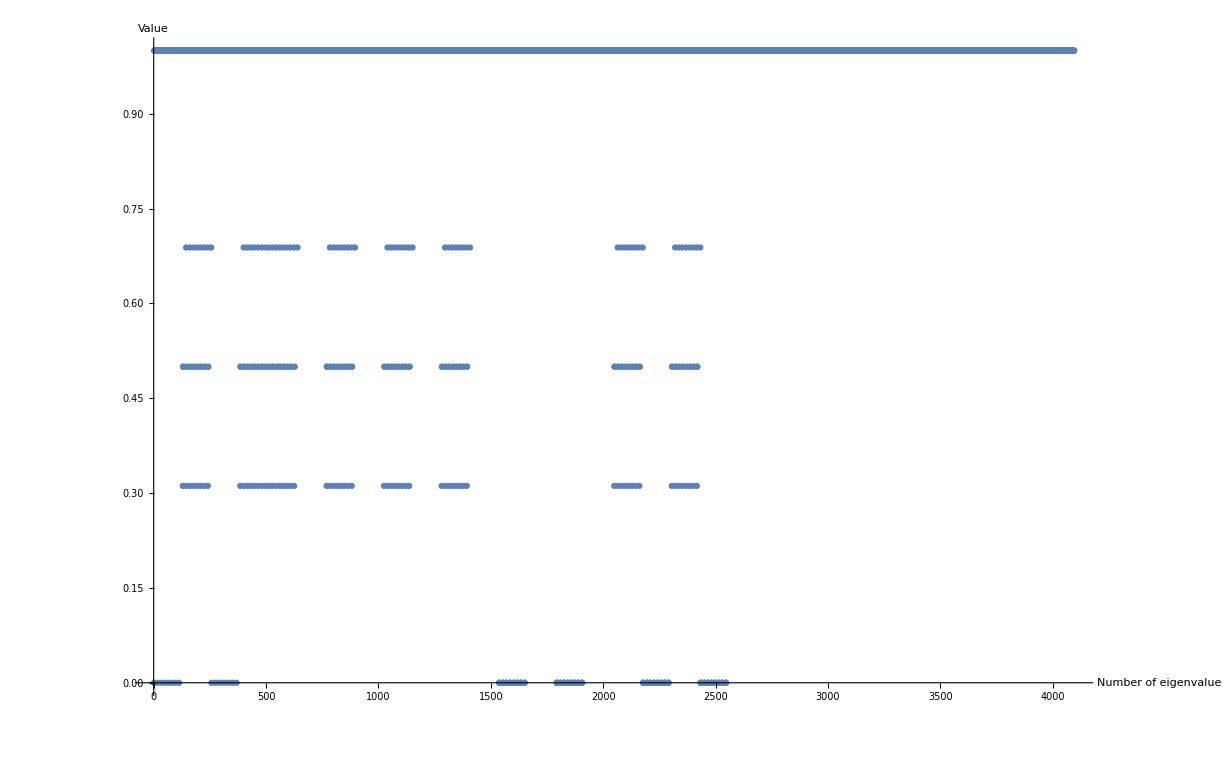

```mathematica
ListPlot[FullHEigenvaluesNum,AxesLabel->{"Number of eigenvalue","Value"}]
```

```mathematica
(*Check if the full Hamiltonian has eigenstates with zero energy*)
MemberQ[QuickDiagonalize[FullHamiltonian,16],0]
```

True

```mathematica
(*Compute eigenvalues of excited states*)
DeleteDuplicates[DeleteCases[DeleteCases[FullHEigenvalues,0],1]]
```

{b^2/(2 (2+b^2)),1/2,(4+b^2)/(2 (2+b^2))}

```mathematica
(*Blocks in Hamiltonian which correspond to the excitations*)
```

```mathematica
DeleteDuplicates[Ceiling[Position[FullHEigenvalues,(4+b^2)/(2 (2+b^2))]/16]]
```

{{9},{10},{11},{12},{13},{14},{15},{16},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{49},{50},{51},{52},{53},{54},{55},{56},{65},{66},{67},{68},{69},{70},{71},{72},{81},{82},{83},{84},{85},{86},{87},{88},{129},{130},{131},{132},{133},{134},{135},{136},{145},{146},{147},{148},{149},{150},{151},{152}}

```mathematica
DeleteDuplicates[Ceiling[Position[FullHEigenvalues,b^2/(2 (2+b^2))]/16]]
```

{{9},{10},{11},{12},{13},{14},{15},{16},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{49},{50},{51},{52},{53},{54},{55},{56},{65},{66},{67},{68},{69},{70},{71},{72},{81},{82},{83},{84},{85},{86},{87},{88},{129},{130},{131},{132},{133},{134},{135},{136},{145},{146},{147},{148},{149},{150},{151},{152}}

```mathematica
DeleteDuplicates[Ceiling[Cases[Position[FullHEigenvalues,1/2],Except[{_,1}]]/16]]
```

{{9},{10},{11},{12},{13},{14},{15},{16},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{49},{50},{51},{52},{53},{54},{55},{56},{65},{66},{67},{68},{69},{70},{71},{72},{81},{82},{83},{84},{85},{86},{87},{88},{129},{130},{131},{132},{133},{134},{135},{136},{145},{146},{147},{148},{149},{150},{151},{152}}

```mathematica
(*Plaquette configurations which correspond to the excitations*)
```

```mathematica
TorusConfiguration[Position_]:=Module[{P1,P4,i1,i2,i3,i4,e1,e2,e3,e4,e5,e6,e7,e8,PlaquetteConfig,PlaquetteList,i,Plaquette},
P1=eListPlaquette1[[Position]];
P4=eListPlaquette4[[Position]];
i1=P4[[3]];
i2=P4[[5]];
i3=P4[[2]];
i4=P4[[1]];
e1=P1[[1]];
e2=P1[[2]];
e3=P1[[3]];
e4=P1[[4]];
e5=P1[[5]];
e6=P1[[6]];
e7=P1[[7]];
e8=P1[[8]];
PlaquetteConfig={i1,i2,i3,i4,e1,e2,e3,e4,e5,e6,e7,e8};
PlaquetteList={Graphics[{Thick,Red,Line[{{1,1},{0,1}}]}](*i1*),Graphics[{Thick,Red,Line[{{0,1},{0,0}}]}](*i2*),Graphics[{Thick,Red,Line[{{0,0},{1,0}}]}](*i3*),Graphics[{Thick,Red,Line[{{1,0},{1,1}}]}](*i4*),Graphics[{Thick,Red,Line[{{0,1},{0,1.5}}]}](*e1*),Graphics[{Thick,Red,Line[{{0,1},{-0.5,1}}]}](*e2*),Graphics[{Thick,Red,Line[{{0,0},{-0.5,0}}]}](*e3*),Graphics[{Thick,Red,Line[{{0,0},{0,-0.5}}]}](*e4*),Graphics[{Thick,Red,Line[{{1,0},{1,-0.5}}]}](*e5*),Graphics[{Thick,Red,Line[{{1,0},{1.5,0}}]}](*e6*),Graphics[{Thick,Red,Line[{{1,1},{1.5,1}}]}](*e7*),Graphics[{Thick,Red,Line[{{1,1},{1,1.5}}]}](*e8*)};
Plaquette={Graphics[{Dashed,Line[{{1,1},{0,1}}]}](*i1*),Graphics[{Dashed,Line[{{0,1},{0,0}}]}](*i2*),Graphics[{Dashed,Line[{{0,0},{1,0}}]}](*i3*),Graphics[{Dashed,Line[{{1,0},{1,1}}]}](*i4*),Graphics[{Dashed,Line[{{0,1},{0,1.5}}]}](*e1*),Graphics[{Dashed,Line[{{0,1},{-0.5,1}}]}](*e2*),Graphics[{Dashed,Line[{{0,0},{-0.5,0}}]}](*e3*),Graphics[{Dashed,Line[{{0,0},{0,-0.5}}]}](*e4*),Graphics[{Dashed,Line[{{1,0},{1,-0.5}}]}](*e5*),Graphics[{Dashed,Line[{{1,0},{1.5,0}}]}](*e6*),Graphics[{Dashed,Line[{{1,1},{1.5,1}}]}](*e7*),Graphics[{Dashed,Line[{{1,1},{1,1.5}}]}](*e8*)};
For[i=1,i≤Length[PlaquetteConfig],i++,
If[PlaquetteConfig[[i]]==1,
Plaquette=ReplacePart[Plaquette,i->PlaquetteList[[i]]];
](*If*);
](*For*);
Show[Plaquette]
](*Module*);
```

```mathematica
(*physical configurations*)
ConfigOf[Eigenvalue_]:=Module[{PosList,PlotList,i},
PosList=DeleteDuplicates[Ceiling[Cases[Position[FullHEigenvalues,Eigenvalue],Except[{_,1}]]/16]];
PlotList={};
For[i=1,i≤Length[PosList],i++,
AppendTo[PlotList,TorusConfiguration[PosList[[i]]/.{polys__}:>(polys)]]
](*For*);
PlotList=DeleteDuplicates[PlotList];
Print[PlotList]
](*Module*)
```

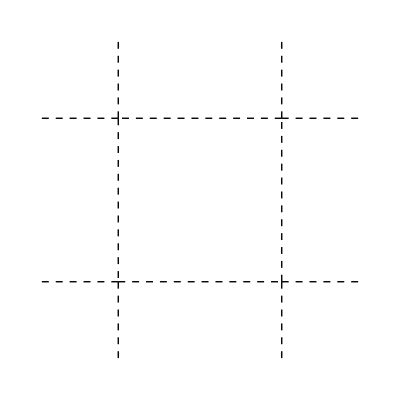
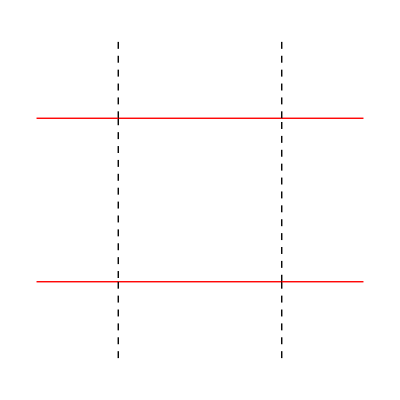
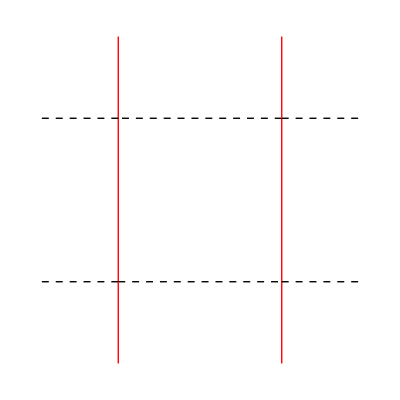

```mathematica
(*Ground states*)
ConfigOf[0]
```

```mathematica
(*Excitations*)
```

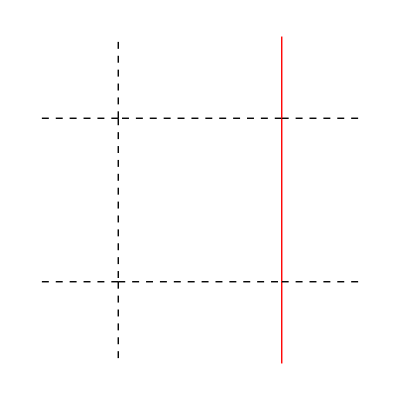
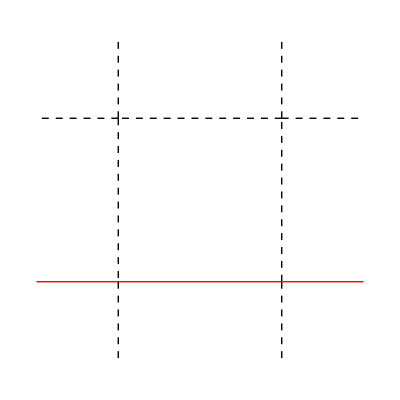
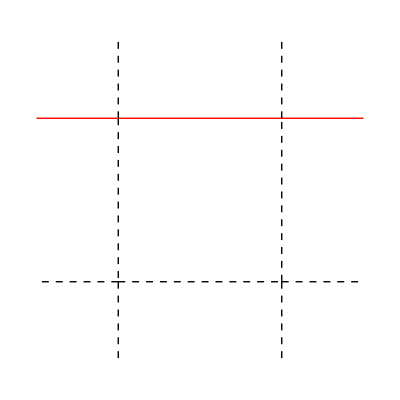
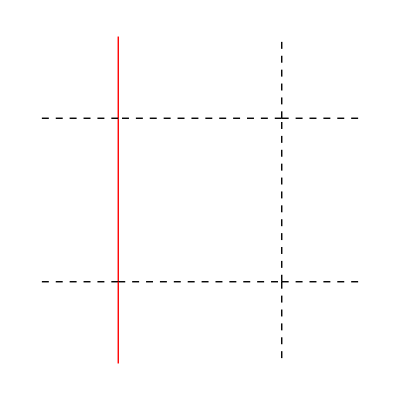

```mathematica
ConfigOf[b^2/(2 (2+b^2))]
```

```mathematica
ConfigOf[(4+b^2)/(2 (2+b^2))]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ConfigOf[1/2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}